```mathematica
计算近地点,远地点,半长轴,半短轴
```

Energy: -14.4445  Angular momenfigm: 7.15

eccentricity: 0.228914  half-long-axis: 1.36656

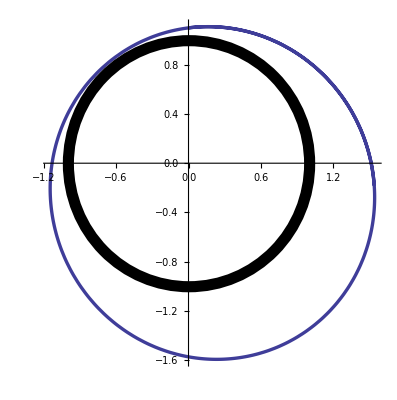

{1.67938,{t→0.68917}}

apogee: 1.06295,-1.30018

{1.05373,{t→1.48792}}

perigee: -0.666952,0.8158

{t→0.231592}

a= 1.36656  b= 1.33027

```mathematica
tm=2.0;coef=4.0 π^2;
xinitial={0,6.5};yinitial={1.1,0.8};
(*.....some theoretical parameters......*)
energy=-4 π^2/yinitial[[1]]+
(xinitial[[2]]^2+yinitial[[2]]^2)/2;
Angularmomenfigm=
yinitial[[1]]*xinitial[[2]]-
xinitial[[1]]*yinitial[[2]];
Print["Energy: ",energy,"  ",
"Angular momenfigm: ",Abs[Angularmomenfigm]]
factor=√(1+2/(2π)^4 energy*Angularmomenfigm^2);
a=-2 π^2/energy;
Print["eccentricity: ",factor,"  ",
"half-long-axis: ",a]
(*.........solving orbit..........*)
equ={x''[t]==-(coef*x[t])/((x[t]^2+y[t]^2)^(3/2)),
y''[t]==-(coef*y[t])/((x[t]^2+y[t]^2)^(3/2)),
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equ,{x,y},{t,0,tm}];
{x,y}={x,y}/.s[[1]];
ParametricPlot[{x[t],y[t]},{t,0,tm},
PlotStyle->Thickness[0.006],
AxesStyle->Thickness[0.003],
BaseStyle->{FontSize->13},
Epilog->{Thickness[0.02],Circle[{0,0},1]}]
(*...calculating parameters through orbit...*)
r[t_]:=√(x[t]^2+y[t]^2);
apogee=FindMaximum[r[t],{t,0.5}]
{x1,y1}=
{x[t/.apogee[[2]]],y[t/.apogee[[2]]]};
Print["apogee: ",x1,",",y1]
perigee=FindMinimum[r[t],{t,1}]
{x2,y2}=
{x[t/.perigee[[2]]],y[t/.perigee[[2]]]};
Print["perigee: ",x2,",",y2]
a=(apogee[[1]]+perigee[[1]])/2;
slope[t_]:=y'[t]/x'[t];aslope=(y2-y1)/(x2-x1);
p=FindRoot[slope[t]==aslope,{t,0.25}]
{x3,y3}={x[t/.p],y[t/.p]};
b=√((y3-y1)^2+(x3-x1)^2-a^2);
Print["a= ",a,"  ","b= ",b]
Clear[x,y,a,b,slope,tm,energy,coef,s,equ]
```